```mathematica
<<HokahokaW`
```

HokahokaW`
(origin)[https://ktakagaki@github.com/ktakagaki/HokahokaW.git]
current Git HEAD:  13ddb7cc898ce8f990bcd7062e894fd2ef4ee0a2
newest file:  Mon 6 Oct 2014 17:18:44

```mathematica
?HHThreshold
```

Takes a trace and returns timepoints at which it crosses threshold.

## Test Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\prog\wb\HokahokaW-dev\Tests

```mathematica
(*BinaryWrite["HHThresholdTest_test1.bin", test1, "Real32"]*)
```

```mathematica
"HHThresholdTest_test1.bin"
```

```mathematica
(*BinaryWrite["HHThresholdTest_test2.bin", test2, "Real32"]*)
```

```mathematica
"HHThresholdTest_test2.bin"
```

```mathematica
test1=BinaryReadList["HHThresholdTest_test1.bin", "Real32"];
test2=BinaryReadList["HHThresholdTest_test2.bin", "Real32"];
```

## Tests

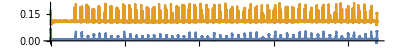

```mathematica
ListLinePlot[{test1,test2}+{0,0.1}, AspectRatio->1/50,PlotRange->All]
```

```mathematica
HHStandardDeviationMedianEstimate[test1]
```

0.00108522

```mathematica
StandardDeviation[test1]
```

0.00609419

```mathematica
HHThreshold[test1]
```

{37,44,3352,3405,4188,4241,5010,5063,5805,5858,6576,6629,7373,7426,8202,8255,9046,9099,9894,9948,10711,10765,11538,11591,12334,12387,13099,13152,13658,13659,13900,13953,14736,14789,15537,15590,16335,16389,17117,17170,17909,17962,18670,18724,19497,19550,20328,20381,21128,21181,21969,22022,22802,22856,23619,23672,23940,23941,24382,24435,25235,25288,25386,25387,26090,26143,26861,26914,27689,27742,28235,28236,28490,28491,28542,28595,29334,29387,30159,30212,30511,30512,30814,30815,30932,30985,31781,31835,32626,32679,33474,33527,33933,33934,34256,34310,34679,34680,35080,35133,35679,35680,35931,35984,36212,36213,36696,36749,37338,37339,37534,37587,38213,38214,38357,38410,39142,39194,39802,39803,39981,40034,40489,40490,40757,40810,40913,40914,41526,41579,41749,41750,41846,41847,42338,42391,42772,42773,43094,43147,43369,43370,43855,43900}

```mathematica
ListLinePlot[ test1, GridLines->{HHThreshold[test1, Automatic],None}, AspectRatio->1/50,PlotRange->All]
```

```mathematica
HHDetectTrain[test1,Automatic]
```

{{37,44},{3352,3405},{4188,4241},{5010,5063},{5805,5858},{6576,6629},{7373,7426},{8202,8255},{9046,9099},{9894,9948},{10711,10765},{11538,11591},{12334,12387},{13099,13152},{13658,13659},{13900,13953},{14736,14789},{15537,15590},{16335,16389},{17117,17170},{17909,17962},{18670,18724},{19497,19550},{20328,20381},{21128,21181},{21969,22022},{22802,22856},{23619,23672},{23940,23941},{24382,24435},{25235,25288},{25386,25387},{26090,26143},{26861,26914},{27689,27742},{28235,28236},{28490,28491},{28542,28595},{29334,29387},{30159,30212},{30511,30512},{30814,30815},{30932,30985},{31781,31835},{32626,32679},{33474,33527},{33933,33934},{34256,34310},{34679,34680},{35080,35133},{35679,35680},{35931,35984},{36212,36213},{36696,36749},{37338,37339},{37534,37587},{38213,38214},{38357,38410},{39142,39194},{39802,39803},{39981,40034},{40489,40490},{40757,40810},{40913,40914},{41526,41579},{41749,41750},{41846,41847},{42338,42391},{42772,42773},{43094,43147},{43369,43370},{43855,43900}}

```mathematica
HHDetectTrain[test1,Automatic, HHTrainBlackout->50, HHTrainPulseLengthMinimum->5]
```

{{3352,3405},{4188,4241},{5010,5063},{5805,5858},{6576,6629},{7373,7426},{8202,8255},{9046,9099},{9894,9948},{10711,10765},{11538,11591},{12334,12387},{13099,13152},{13900,13953},{14736,14789},{15537,15590},{16335,16389},{17117,17170},{17909,17962},{18670,18724},{19497,19550},{20328,20381},{21128,21181},{21969,22022},{22802,22856},{23619,23672},{24382,24435},{25235,25288},{26090,26143},{26861,26914},{27689,27742},{28542,28595},{29334,29387},{30159,30212},{30932,30985},{31781,31835},{32626,32679},{33474,33527},{34256,34310},{35080,35133},{35931,35984},{36696,36749},{37534,37587},{38357,38410},{39142,39194},{39981,40034},{40757,40810},{41526,41579},{42338,42391},{43094,43147},{43855,43900}}

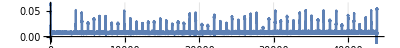

```mathematica
ListLinePlot[ test1, GridLines->{Flatten[HHDetectTrain[test1,Automatic, HHTrainBlackout->50, HHTrainPulseLengthMinimum->5]],None}, AspectRatio->1/50,PlotRange->All]
```

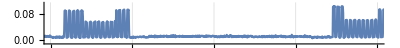

```mathematica
ListLinePlot[ test2, GridLines->{Flatten[HHDetectTrain[test2,Automatic, HHTrainBlackout->50, HHTrainPulseLengthMinimum->5]],None}, AspectRatio->1/50,PlotRange->{{4000,5000},All}]
```